# Практикум № 3

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр. Ковалевская В.С.
  16 сентября 2021

```mathematica
A={xA,yA} 
B={xB,yB}
```

{xA,yA}

{xB,yB}

```mathematica
0.5(A+B)
```

{0.5 (xA+xB),0.5 (yA+yB)}

```mathematica
A*B
```

{xA xB,yA yB}

```mathematica
A==B
```

{xA,yA}=={xB,yB}

```mathematica
A=B
```

{xB,yB}

```mathematica
AB=B-A
```

{0,0}

```mathematica
{x,y}.{x,y}
```

x^2+y^2

```mathematica
√(#.#)&[B-A]
```

0

## Задание 1

Задайте координаты произвольного треугольника и изобразите его. Подпишите его вершины. Определите функцию, которая создает графические примитивы, необходимые для отображения произвольного треугольника.

```mathematica
points={{0,-2},{1,4},{-1,2}}
```

{{0,-2},{1,4},{-1,2}}

```mathematica
Graphics[Polygon[points],ImageSize->100]
```

-Graphics-

```mathematica
Graphics[{FaceForm[White], EdgeForm[Directive[Thick,Black]],Polygon[points]},ImageSize->100]
```

-Graphics-

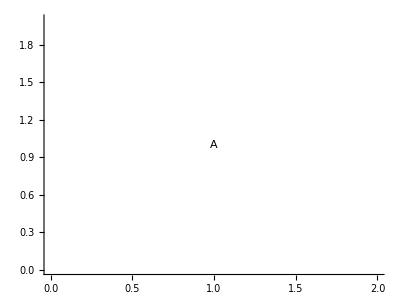

```mathematica
Graphics[Text["A",{1,1}],Axes->True]
```

```mathematica
MapThread[Text[#1,#2]&,{{"A","B","C"},points+0.1}]
```

{Text[A,{0.1,-1.9}],Text[B,{1.1,4.1}],Text[C,{-0.9,2.1}]}

```mathematica
Graphics[{FaceForm[White], EdgeForm[Directive[Thick,Black]],Polygon[points], MapThread[Text[#1,#2]&,{{"A","B","C"},points+0.1}]},ImageSize->100]
```

-Graphics-

```mathematica
triangle[pts_List]:={FaceForm[White], EdgeForm[Directive[Thick,Black]],Polygon[pts], MapThread[Text[#1,#2]&,{{"A","B","C"},pts+0.1}]}
```

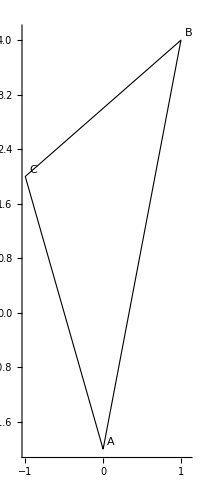

```mathematica
Graphics[triangle[points],Axes->True]
```

## Задание 2

Реализуйте функцию для указания в графической области величины площади треугольника . Площадь должна вычисляться отдельной функцией .

```mathematica
points//Flatten
```

{0,-2,1,4,-1,2}

```mathematica
(√(#.#)&[points[[2]]-points[[1]]]+√(#.#)&[points[[2]]-points[[3]]]+√(#.#)&[points[[3]]-points[[1]]])/2
```

1/2 (2 √2+√17+√37)

```mathematica
√(#.#)&[points[[2]]-points[[1]]]
```

√37

```mathematica
√(#.#)&[points[[2]]-points[[3]]]
```

2 √2

```mathematica
√(#.#)&[points[[3]]-points[[1]]]
```

√17

```mathematica
polPerimetr[points_]:=With[{a=√(#.#)&[points[[2]]-points[[1]]],b=√(#.#)&[points[[2]]-points[[3]]],c=√(#.#)&[points[[3]]-points[[1]]]}, {(a+b+c)/2, a, b, c}](*функция, которая вычисляет полупериметр и длины сторон треугольника по заданным координатам вершин треугольника*)
```

```mathematica
polPerimetr[points]
```

{1/2 (2 √2+√17+√37),√37,2 √2,√17}

```mathematica
trArea[points_]:=With[{a=polPerimetr[points][[2]],b=polPerimetr[points][[3]],c=polPerimetr[points][[4]],p=polPerimetr[points][[1]]},√(p (p-a) (p-b) (p-c))](*функция, которая по заданным координатам вершин треугольника, вычисляет площадь этого треугольника по формуле Герона*)
```

```mathematica
trArea[points]//N
```

5.

## Задание 3

Изобразите треугольник и произвольную медиану\медианы . Координаты начала и конца медианы вычислите в отдельной функции .

```mathematica
points={{0,-2},{1,4},{-1,2}}
```

{{0,-2},{1,4},{-1,2}}

```mathematica
DeleteCases[points, points[[1]]]
```

{{1,4},{-1,2}}

```mathematica
DeleteCases[points, points[[1]]]//Flatten
```

{1,4,-1,2}

```mathematica
Plus@@(DeleteCases[{{1,1},{1,5},{5,4}},{1,1}])
```

{6,9}

```mathematica
(Plus@@(DeleteCases[{{1,1},{1,5},{5,4}},{1,1}]))/2
```

{3,9/2}

```mathematica
findMedian[points_(*координаты вершин трегольника*),vertex_(*координаты вершины, из которой опускаем медиану*)]:=With[{vect=DeleteCases[points,vertex]//Flatten},{vertex,{(vect[[3]]+vect[[1]])/2,(vect[[4]]+vect[[2]])/2(*координаты медианы треугольника*)}}]
```

```mathematica
findMedian[points,points[[1]]]
```

{{0,-2},{0,3}}

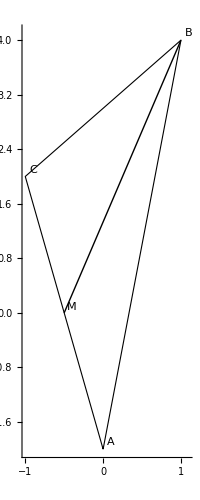

```mathematica
Graphics[{triangle[points], Line[findMedian[points,points[[2]]]],Text["M",(findMedian[points,points[[2]]]//Last)+0.09]},Axes->True]
```

```mathematica
median[points_,vertex_]:={Thick,Orange,Line[findMedian[points,vertex]],PointSize[0.03],Point[findMedian[points,vertex]//Last],Text["M",(findMedian[points,vertex]//Last)-0.15]}
```

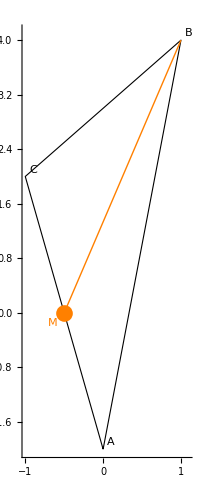

```mathematica
Graphics[{triangle[points],median[points, points[[2]]]}, Axes->True, AspectRatio->Automatic]
```

## Задание 4

Изобразите треугольник и произвольную высоту\высоты.
Координаты начала и конца высоты вычислите в отдельной функции.

```mathematica
points={{0,-2},{1,4},{-1,2}}
```

{{0,-2},{1,4},{-1,2}}

```mathematica
buildLineequation[point_List,vect_List]:=(x-point⟦1⟧)*vect⟦2⟧== (y-point⟦2⟧)*vect⟦1⟧(*функция для построения уравнения прямой по точке и направляющему отрезку*)
```

```mathematica
buildLineequation[{1,1},{3,4}]
```

4 (-1+x)==3 (-1+y)

```mathematica
findAltitude[points_,vertex_]:=With[{vect=(Plus@@(DeleteCases[points,vertex]*{1,-1})),
vectNormal=Reverse[{1,-1}*(Plus@@(DeleteCases[points, vertex]*{1,-1}))]},{vertex,({x,y}/.Solve[{buildLineequation[vertex,vectNormal],buildLineequation[DeleteCases[points,vertex]//First,vect]},{x,y}])//Flatten}]
```

```mathematica
findAltitude[points,points[[1]]]
```

{{0,-2},{-5/2,1/2}}

```mathematica
attitude[points_,vertex_]:={Thick,Green,Line[findAltitude[points,vertex]],PointSize[0.03],Point[findAltitude[points,vertex]//Last],Text["H",(findAltitude[points,vertex]//Last)-0.15]}
```

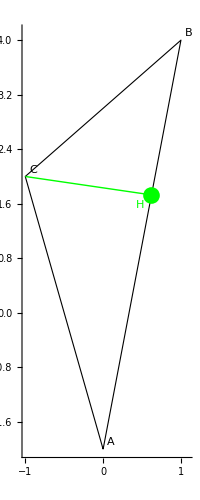

```mathematica
Graphics[{triangle[points],attitude[points, points[[3]]]}, Axes->True, AspectRatio->Automatic]
```

## Задание 5

Изобразите треугольник и произвольную биссектрису\биссектрисы.

```mathematica
points={{0,-2},{1,4},{-1,2}}
```

{{0,-2},{1,4},{-1,2}}

```mathematica
getRelation [points_, vertex_] := With[{pt = DeleteCases[points, vertex] // Flatten}, (√((vertex⟦1⟧ - pt⟦3⟧)^2+(vertex⟦2⟧-pt⟦4⟧)^2))/(√((vertex⟦1⟧ - pt⟦1⟧)^2+(vertex⟦2⟧-pt⟦2⟧)^2))]
```

```mathematica
getRelation[points,points[[1]]]
```

√(17/37)

```mathematica
findBisectriss[points_,vertex_]:=With[{point=DeleteCases[points,vertex]//Flatten,bis=getRelation [points, vertex]},
{vertex,{(point⟦3⟧+bis point⟦1⟧)/(1 + bis) , (point⟦4⟧+bis point⟦2⟧)/(1 + bis) }}](*функция, которая возвращает координаты вершины треугольника, из которой будет проводится биссектриса и которая вычисляет координаты основания биссектрисы*)
```

```mathematica
findBisectriss[points,points[[2]]]
```

{{1,4},{-1/(1+2 √(2/37)),(2-4 √(2/37))/(1+2 √(2/37))}}

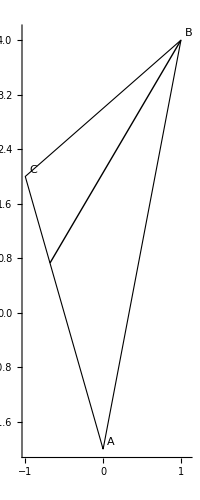

```mathematica
Graphics[{triangle[points], Line[findBisectriss[points,points[[2]]]]},Axes->True]
```

```mathematica
bisectriss[points_,vertex_]:={Thick,Purple,Line[findBisectriss[points,vertex]],PointSize[0.03],Point[findBisectriss[points,vertex]//Last], Text["K",(findBisectriss[points,vertex]//Last)-0.15]}
```

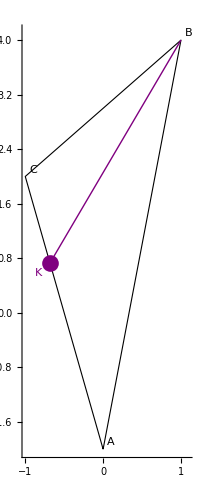

```mathematica
Graphics[{triangle[points],bisectriss[points, points[[2]]]}, Axes->True, AspectRatio->Automatic]
```

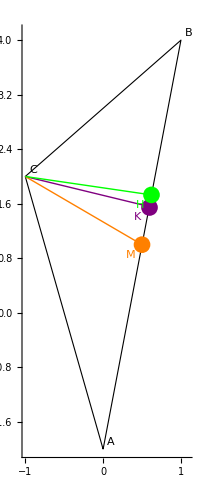

```mathematica
Graphics[{triangle[points],bisectriss[points, points[[3]]],median[points, points[[3]]],attitude[points, points[[3]]]}, Axes->True, AspectRatio->Automatic]
```

## Задание 6

Отобразите на графике окружность, описанную около треугольника.

```mathematica
getoutR[points_]:=With[{a=polPerimetr[points][[2]],b=polPerimetr[points][[3]],c=polPerimetr[points][[4]], S=trArea[points]}, (a b c)/(4 S)](*нашли радиус описанной около треугольника окружности*)
```

```mathematica
R=getoutR[points]
```

√(629/((2 √2+√17+√37) (-2 √2+1/2 (2 √2+√17+√37)) (-√17+1/2 (2 √2+√17+√37)) (-√37+1/2 (2 √2+√17+√37))))

```mathematica
coord=points//Flatten
```

{0,-2,1,4,-1,2}

```mathematica
(coord⟦1⟧ - x)^2+(coord⟦2⟧ - y)^2 == (getoutR[points])^2(*уравнение окружности*)
```

x^2+(-2-y)^2==629/((2 √2+√17+√37) (-2 √2+1/2 (2 √2+√17+√37)) (-√17+1/2 (2 √2+√17+√37)) (-√37+1/2 (2 √2+√17+√37)))

```mathematica
(coord⟦3⟧ - x)^2+(coord⟦4⟧ - y)^2 == (getoutR[points])^2
```

(1-x)^2+(4-y)^2==629/((2 √2+√17+√37) (-2 √2+1/2 (2 √2+√17+√37)) (-√17+1/2 (2 √2+√17+√37)) (-√37+1/2 (2 √2+√17+√37)))

```mathematica
Solve[(coord⟦1⟧ - x)^2+(coord⟦2⟧ - y)^2 == (getoutR[points])^2&&(coord⟦3⟧ - x)^2+(coord⟦4⟧ - y)^2 == (getoutR[points])^2&&(coord⟦5⟧ - x)^2+(coord⟦6⟧ - y)^2 == (getoutR[points])^2,{x,y}](*здесь - {x, y} - координаты центра описанной около треугольника окружности*)
```

{{x→23/10,y→7/10}}

```mathematica
Solve[(coord⟦1⟧ - x)^2+(coord⟦2⟧ - y)^2 == (getoutR[points])^2&&(coord⟦3⟧ - x)^2+(coord⟦4⟧ - y)^2 == (getoutR[points])^2,{x,y}]//Values(*получаем значения из списка правил *)
```

{{23/10,7/10},{-13/10,13/10}}

```mathematica
getoutCenter[points_] := With[{cords = points // Flatten, R = getoutR[points]},
Solve[(cords⟦1⟧ - a)^2+(cords⟦2⟧ - b)^2 == R^2&&(cords⟦3⟧ - a)^2+(cords⟦4⟧ - b)^2 == R^2&&(cords⟦5⟧ - a)^2+(cords⟦6⟧ - b)^2 == R^2, {a, b} ]// Values // First
]
```

```mathematica
getoutCenter[points]
```

{23/10,7/10}

```mathematica
outCircle[points_] := {Thick,Cyan, Circle[getoutCenter[points], getoutR[points]], PointSize[0.02], Point[getoutCenter[points]],Text["O",getoutCenter[points]-0.15]}
```

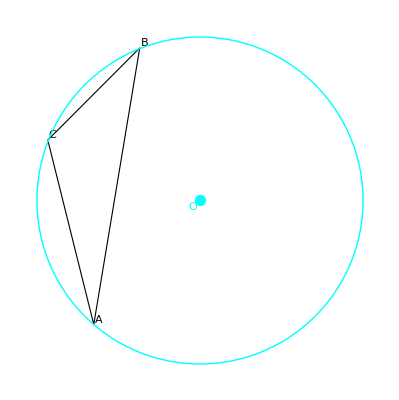

```mathematica
Graphics[{triangle[points], outCircle[points]}]
```

## Задание 7

Отобразите на графике окружность, вписанную в треугольник

```mathematica
points//Flatten
```

{0,-2,1,4,-1,2}

```mathematica
points
```

{{0,-2},{1,4},{-1,2}}

```mathematica
getRadius[points_]:=With[{a=polPerimetr[points][[2]],b=polPerimetr[points][[3]],c=polPerimetr[points][[4]], S=trArea[points]}, (2 S)/(a+b+c)](*функция, которая вычисляет радиус вписанной в треугольник окружности по координатам вершин треугольника*)
```

```mathematica
getRadius[points]//N
```

0.767207

```mathematica
getCenter[points_]:=With[{a=polPerimetr[points][[2]],b=polPerimetr[points][[3]],c=polPerimetr[points][[4]], pt=points//Flatten},{(pt[[5]] a+pt[[1]] b+pt[[3]] c)/(a+b+c),(pt[[6]] a+pt[[2]] b+pt[[4]] c)/(a+b+c)}](*функция, которая вычисляет координаты центра вписанной в треугольник окружности по координатам вершин треугольника*)
```

```mathematica
getCenter[points]
```

{(√17-√37)/(2 √2+√17+√37),(-4 √2+4 √17+2 √37)/(2 √2+√17+√37)}

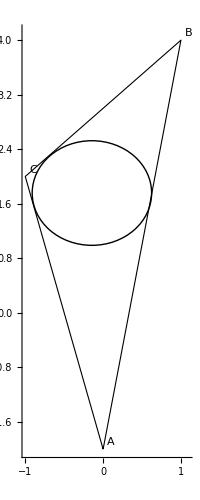

```mathematica
Graphics[{triangle[points], Circle[getCenter[points],getRadius[points]]},Axes->True,AspectRatio->Automatic]
```

```mathematica
inCircle[points_]:= {Thick,Pink,Circle[getCenter[points],getRadius[points]],Point[getCenter[points]],Text["P",getCenter[points]-0.15]}
```

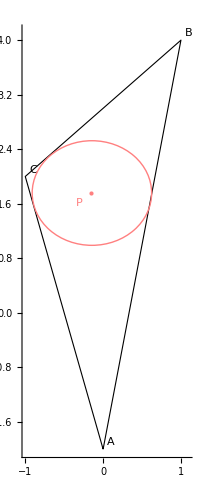

```mathematica
Graphics[{triangle[points], inCircle[points]},Axes->True,AspectRatio->Automatic]
```

## Задание 8

Используя функцию Manipulate, создайте финальный пользовательский интерфейс .

```mathematica
Manipulate[Graphics[{triangle[points],Blue,Text[s[points],{1,2}],f[points,points⟦i⟧],If[t,outCircle[points]],If[z,inCircle[points]]},Axes->True,AspectRatio->Automatic],{f,{median,attitude,bisectriss}},{i,{1->"A",2->"B",3->"C"}},{{t,False,"outCircle"},{True,False}},{{z,False,"inCircle"},{True,False}}]
```

Part::partd: Part specification points⟦3⟧ is longer than depth of object.